```mathematica
FullSimplify[DSolve[y'[x]+(x+(1+3 x^2)/(1+x+x^3)) y[x] == x^3+2x+x^2(1+3 x^2)/(1+x+x^3),y[x],x]]
```

{{y[x]→x^2+(ⅇ^(-x^2/2) C[1])/(1+x+x^3)}}

```mathematica
FullSimplify[D[x^2+(ⅇ^(-x^2/2))/(1+x+x^3),x]]
```

2 x-(ⅇ^(-x^2/2) (1+x+4 x^2+x^4))/((1+x+x^3)^2)

```mathematica
FullSimplify[D[x^2+(ⅇ^(-x^2/2))/(1+x+x^3),{x,2}]]
```

2+(ⅇ^(-x^2/2) (1+x (-6+x (8+x (6+x (19+x (2+7 x+x^3)))))))/((1+x+x^3)^3)

```mathematica
ya[x_]:=(ⅇ^(-x^2/2))/(1+x+x^3)+x^2
```

```mathematica
dyadx[x_]:=2 x-(ⅇ^(-x^2/2) (1+3 x^2))/((1+x+x^3)^2)-(ⅇ^(-x^2/2) x)/(1+x+x^3)
```

```mathematica
d2yadx2[x_]:=2+(ⅇ^(-x^2/2) (1+x (-6+x (8+x (6+x (19+x (2+7 x+x^3)))))))/((1+x+x^3)^3)
```

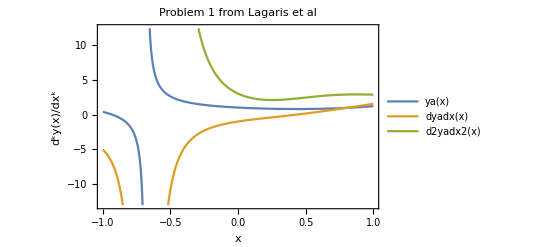

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,-1,1},AxesLabel->{"x","d^ky(x)/dx^k"},PlotLegends->"Expressions",PlotLabel->"Problem 1 from Lagaris et al",Frame->True]
```